```mathematica
Needs["CustomTicks`"]
(* Set default plot options *)
defaultPlotOptions={Frame->True,Axes->False,LabelStyle->{Black,FontFamily->"Arial",FontSize->16},FrameStyle->Directive[Black,Thickness[0.002]],ImageSize->Large};
SetOptions[ListPlot,defaultPlotOptions];
SetOptions[ListLogPlot,defaultPlotOptions];
SetOptions[ListLogLogPlot,defaultPlotOptions];
SetOptions[ListLogLinearPlot,defaultPlotOptions];
SetOptions[Plot,defaultPlotOptions];
SetOptions[LogPlot,defaultPlotOptions];
SetOptions[LogLinearPlot,defaultPlotOptions];
SetOptions[LogLogPlot,defaultPlotOptions];
SetOptions[ListContourPlot,{Frame->True,Axes->False,LabelStyle->{Black,FontFamily->"Arial",FontSize->16},FrameStyle->Directive[Black,Thickness[0.002]],ContourStyle->Black,ImageSize->Large,AspectRatio->1/GoldenRatio}];

(* Define color scheme *)
tempGradient[nCols_]:=Table[ColorData[{"CandyColors","Reverse"}][i],{i,0,1,1/(nCols-1)}]
```

```mathematica
temps385={0.000036,0.000045,0.000054,0.000077,0.000091,0.00014,0.00025,0.00033,0.0005,0.001,0.002,0.0025,0.00385,0.005,0.01,0.016,0.039};
cols385=tempGradient[Length[temps385]]

temps380={0.0022,0.0028,0.00385,0.005,0.0063,0.01,0.016,0.025,0.039,0.063};
cols380=tempGradient[Length[temps380]]
```

{RGBColor[0.659388, 0.872053, 0.882048],RGBColor[0.666336, 0.85163, 0.8957745],RGBColor[0.673284, 0.831207, 0.909501],RGBColor[0.6846915, 0.7802425, 0.8848445],RGBColor[0.696099, 0.729278, 0.860188],RGBColor[0.7311225, 0.6850045, 0.819293],RGBColor[0.766146, 0.640731, 0.778398],RGBColor[0.7987145, 0.5869310000000001, 0.720527],RGBColor[0.831283, 0.533131, 0.662656],RGBColor[0.8307375, 0.46292900000000003, 0.593907],RGBColor[0.830192, 0.392727, 0.525158],RGBColor[0.7844175, 0.329411, 0.466507],RGBColor[0.738643, 0.266095, 0.407856],RGBColor[0.6596935, 0.24196800000000002, 0.38151650000000004],RGBColor[0.580744, 0.217841, 0.355177],RGBColor[0.492966, 0.211095, 0.349283],RGBColor[0.405188, 0.204349, 0.343389]}

{RGBColor[0.659388, 0.872053, 0.882048],RGBColor[0.67174, 0.8357454444444444, 0.9064506666666666],RGBColor[0.691029, 0.7519288888888889, 0.8711464444444444],RGBColor[0.742797, 0.6702466666666667, 0.8056613333333333],RGBColor[0.8023332222222223, 0.5809532222222222, 0.7140968888888889],RGBColor[0.8307981111111111, 0.4707292222222222, 0.6015457777777777],RGBColor[0.7996756666666668, 0.3505163333333334, 0.4860573333333334],RGBColor[0.7035543333333334, 0.2553718888888889, 0.39614955555555553],RGBColor[0.5612377777777778, 0.2163418888888889, 0.3538672222222222],RGBColor[0.405188, 0.204349, 0.343389]}

```mathematica
α2cr385=
```

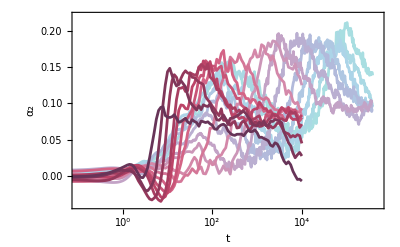

```mathematica
ListPlot[Table[{Log10[α2cr385[[i,j,1]]],α2cr385[[i,j,2]]},{i,Length[α2cr385]},{j,Length[α2cr385[[i]]]}],
PlotRange->{{Log10[0.1],5.7},{-0.04,0.22}},FrameLabel->{{"α_2",None},{"t",None}},
FrameTicks->{Automatic,{LogTicks[10,-2,6],LogTicks[10,-2,6,ShowTickLabels->False]}},
Joined->True,PlotStyle->cols385,ImageSize->400]
```